## DNA λ_s Eigenvalue Analysis

/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T

0.25

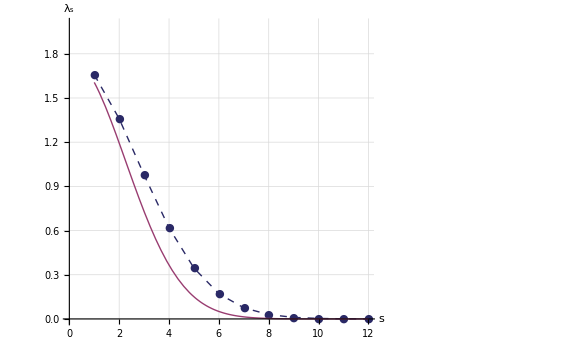

CreateDirectory::filex: "/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T/0.25/" already exists.

/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T/0.25

0.25/lambda_s_L5_m10.pdf

```mathematica
Needs["PlotLegends`"]
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]

L=5;
m=10;
Δ=L/(2 m)//N
σ=1;
κ=1;

LastEval=12;

T[R1_, R2_] := Exp[-(R1 - R2)^2];
MT = Table[Δ T[ Δ R1, Δ R2],{R1, -m, m}, {R2, -m, m}] // N;
Subscript[Mλ, s] = Eigenvalues[MT];
Subscript[MAλ, s][s_]=π^(1/2) Exp[-((π (s))/L)^2/4]//N;
Subscript[dataMAλ, s]=Table[Subscript[MAλ, s][Abs[i]],{i,1,LastEval}];

fsAxesLabel=24;
fs2=18;

p1=ListLinePlot[Subscript[Mλ, s],PlotStyle->{Thick,Dashed,Darker[ColorData[1,1]]},PlotMarkers->{"●"},PlotRange->{{0,20},{0,2}}];
p2=Plot[Subscript[MAλ, s][x],{x,1,LastEval},PlotStyle->{Thick,ColorData[1,2]},AxesOrigin->{0,0},PlotRange->{{0,20},{0,2}}];
{p1,p2};

legend={{Graphics[{Thick,Dashed,Darker[ColorData[1,1]],PointSize[Large],Point[{1,0}],Line[{{0,0},{2,0}}]}],Style["Numerical",FontSize->fs2]},{Graphics[{Thick,ColorData[1,2],Line[{{0,0},{2,0}}]}],Style["Analytical",FontSize->fs2]}};

EvalPlotλ=ShowLegend[Show[{p1,p2},PlotRange->{{0,LastEval},{0,2}},ImageSize->Large,(*PlotLabel->Style["Eigenvalue λ_s Plot (L="<>ToString[L]<>" m="<>ToString[m]<>")",FontSize->fsTitle],*)GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesLabel->{Style["s",FontSize->fsAxesLabel],Style["λ_s",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2},ImageSize->Large],{legend,LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->0.5,LegendPosition->{0.1,0.1}}]
EvalPlotλ2=Magnify[EvalPlotλ,2];
(*Export["lambda_s_L"<>ToString[L]<>"_m"<>ToString[m]<>".png",EvalPlotλ2]*)

CreateDirectory[ToString[Δ]]
Export[ToString[Δ]<>"/lambda_s_L"<>ToString[L]<>"_m"<>ToString[m]<>".pdf",EvalPlotλ]
```

Comparison of Eigenvalues - Numerical and Analytical

```mathematica
(*
5,5
10,10
25,25
50,50

5,10
10,20
25,50
50,100

5,25
10,50
25,125
*)
```

```mathematica
50/(2*250)//N
```

0.1